## init

Set the library’s directory first!

```mathematica
directory="/home/tchr/Projects/Mathematica/MSE-Mathematica/";
Get["mse.m",Path->directory];
```

## Import precomputed data

Set the data’s directory preferably in the variable ‘filename’.

```mathematica
filename="/home/tchr/Projects/Mathematica/MSE-Mathematica/import/round1m1-1.xls.pre.dat";
```

Load the data in variables with meaningful names

```mathematica
import[filename,"precomp"];
{header,noM,noU,noD,noAttr,distanceMatrices,matchMatrix,mate}
```

{{Market,Upstream,DownStream,Distance1,Distance2,Distance3,Match},6,{{{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50}},{{30},{25},{17},{6},{16},{27},{45},{23},{46},{8},{41},{21},{44},{38},{18},{11},{35},{42},{24},{15},{28},{43},{14},{9},{29},{10},{32},{26},{19},{34},{12},{1},{49},{39},{4},{5},{37},{7},{40},{33},{31},{2},{20},{3},{22},{50},{36},{48},{47},{13}}},23,{{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},10,{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50}},{1}}}}
 |  |  |  |

## Routines (calculate payoff matrix, inequalities members, dataArray)

```mathematica
CpayoffMatrix[payoffDM,noM,noU,noD];
```

```mathematica
Cineqmembers[mate];
```

```mathematica
CdataArray[payoffMatrix,Cx[noAttr-1]];
```

## Maximization

```mathematica
seedrandom=4321;
```

The global variable “permuteinvariant” when set to true the order of the attributes is set related to their statistics.

```mathematica
permuteinvariant=True;
```

### Differential Evolution Method

The default DifferentialEvolution parameters:

option name | default value |  
"CrossProbability" | 0.5 | probability that a gene is taken from x_i
"InitialPoints" | Automatic | set of initial points 
"PenaltyFunction" | Automatic | function applied to constraints to penalize invalid points
"PostProcess" | Automatic | whether to post-process using local search methods 
"RandomSeed" | 0 | starting value for the random number generator
"ScalingFactor" | 0.6 | scale applied to the difference vector in creating a mate 
"SearchPoints" | Automatic | size of the population used for evolution 
"Tolerance" | 0.001 | tolerance for accepting constraint violations

```mathematica
?maximize
```

maximize[dataArray_,noAttr_,method_:"DifferentialEvolution", permuteinvariant_:False, printflag_:False] is MSE specific and uses the optimize function. It uses the objective function (that counts the number of satisfied inequalities). It returns a list {max,{x1->value1, x2->value2, ...}, number of inequalities} where max is the maximum number of satisfied inequalities found and the solution of the maximization method {value1,value2,...}

```mathematica
method1={"DifferentialEvolution","CrossProbability"->0.5,"InitialPoints"->Automatic,"PenaltyFunction"->Automatic,"PostProcess"->Automatic,"RandomSeed"->seedrandom,"ScalingFactor"->0.6,"SearchPoints"->Automatic,"Tolerance"->0.001};
sol1=maximize[dataArray,noAttr,method1,permuteinvariant,True];
```

The new ordering of attributes used for calculating the solutio order={2,1}

Method {DifferentialEvolution, CrossProbability -> 0.5, InitialPoints -> Automatic, PenaltyFunction -> Automatic, PostProcess -> Automatic, RandomSeed -> 4321, ScalingFactor -> 0.6, SearchPoints -> Automatic, Tolerance -> 0.001}

Completed : {Number of satisfied inequalities→29966.,{Distance2→3.83928,Distance3→2.93331},Number of inequalities→30625}
Satisfied Ineqs Analysis:
 Market no | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25
Satisfied | 1200 | 1189 | 1205 | 1205 | 1199 | 1197 | 1207 | 1198 | 1198 | 1191 | 1202 | 1201 | 1198 | 1209 | 1197 | 1206 | 1195 | 1196 | 1188 | 1201 | 1187 | 1205 | 1198 | 1203 | 1191
Total | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225
Percentage % | 98 | 97 | 98 | 98 | 98 | 98 | 99 | 98 | 98 | 97 | 98 | 98 | 98 | 99 | 98 | 98 | 98 | 98 | 97 | 98 | 97 | 98 | 98 | 98 | 97

### Particle Swarm Optimization

```mathematica
?pso
```

pso[objFun_,nparts_Integer,bndLo_List,bndUp_List,niter_Integer:100,r_Integer:1]
nparts: the number of particles
bndLo: a list of the lower bounds, one for each dimension
bndUp: a list of the upper bounds, one for each dimension
niter: Number of iterations
r: length of the toroidal neighbour scheme e.g. r=1 gives (i-1 mod nparts, i, i+1 mod nparts) as the neighbours of particle i

```mathematica
method2={"ParticleSwarmOptimization","nparts"->32,"bndLo"->-10,"bndUp"->10,"niter"->200,"r"->1,"RandomSeed"->seedrandom};
sol2=maximize[dataArray,noAttr,method2,permuteinvariant,True];
```

The new ordering of attributes used for calculating the solutio order={2,1}

Method {ParticleSwarmOptimization, nparts -> 32, bndLo -> -10, bndUp -> 10, niter -> 200, r -> 1, RandomSeed -> 4321}

Completed : {Number of satisfied inequalities→29964,{Distance2→3.70796,Distance3→2.69361},Number of inequalities→30625}
Satisfied Ineqs Analysis:
 Market no | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25
Satisfied | 1201 | 1190 | 1206 | 1205 | 1199 | 1198 | 1207 | 1196 | 1197 | 1191 | 1202 | 1200 | 1197 | 1209 | 1196 | 1206 | 1194 | 1195 | 1190 | 1199 | 1186 | 1205 | 1198 | 1204 | 1193
Total | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225
Percentage % | 98 | 97 | 98 | 98 | 98 | 98 | 99 | 98 | 98 | 97 | 98 | 98 | 98 | 99 | 98 | 98 | 97 | 98 | 97 | 98 | 97 | 98 | 98 | 98 | 97

## Confidence Intervals

```mathematica
sol=sol1;method=method1;
(*sol=sol2;method=method2;*)
```

```mathematica
ssSize=3;numSubsamples=50;alpha=0.05;
```

Starting pointIdentified process where alpha = 0.05

{8, 20, 23} {6, 21, 25} {12, 15, 25} {4, 9, 10} {8, 19, 20} {4, 12, 24} {6, 8, 20} {1, 6, 24} {9, 14, 24} {7, 8, 23}
Iterations completed:10
 {2, 3, 8} {1, 2, 19} {4, 6, 13} {6, 21, 22} {3, 10, 20} {13, 16, 25} {2, 7, 9} {3, 9, 13} {1, 3, 10} {8, 24, 25}
Iterations completed:20
 {7, 9, 12} {4, 7, 15} {9, 17, 24} {7, 17, 22} {1, 14, 22} {10, 16, 22} {4, 16, 24} {8, 12, 17} {10, 17, 19} {13, 20, 21}
Iterations completed:30
 {1, 12, 14} {16, 22, 23} {9, 10, 21} {11, 16, 18} {7, 10, 17} {4, 18, 23} {10, 15, 22} {13, 14, 24} {5, 10, 15} {3, 4, 16}
Iterations completed:40
 {5, 9, 19} {11, 14, 18} {9, 17, 25} {5, 13, 17} {9, 13, 16} {4, 8, 18} {3, 7, 20} {4, 12, 23} {6, 10, 24} {15, 18, 21}
Iterations completed:50

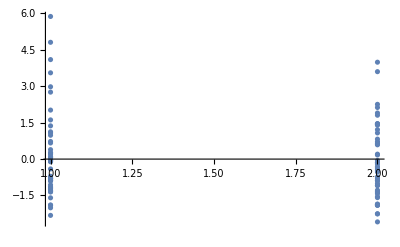
{23.8191,{{{{Symmetric case,{Distance2→{2.43721,5.24134},Distance3→{2.04824,3.81838}}},{Asymmetric case,{Distance2→{2.1935,4.52607},Distance3→{1.70146,3.70485}}}},{{1.12406,1.80697},{-2.31919,-2.58796},{-1.14665,0.587881},{-0.0668686,1.39942},{1.07775,1.89809},{-1.59627,-1.90576},{0.725989,1.44532},{2.01911,-1.28168},{-0.880614,-2.25572},{-0.111529,-0.0619326},{0.0847848,-1.86367},{-1.9037,-1.88682},{-0.861914,-1.08195},{-1.22429,-1.42459},{0.0941209,1.45305},{0.259123,-0.880179},{-1.89084,-1.90202},{-1.31002,-1.37523},{0.981939,-0.411225},{0.388309,-2.25598},{-2.00818,-1.85395},{0.200138,0.20359},{-1.18248,-1.09415},{-1.35447,-0.999864},{-1.34175,-1.58664},{3.55454,-0.354731},{-0.0681161,-0.204926},{-0.791309,0.718818},{-0.805993,1.21268},{1.61437,2.25599},{-0.405976,-0.144485},{-0.874425,-0.464302},{2.98002,3.99201},{0.255049,-0.526311},{-0.814628,0.822608},{-0.08811,0.62026},{4.81227,3.60196},{0.664315,-0.893082},{4.09966,1.46093},{-1.29224,-1.33244},{2.75882,-0.799963},{-0.764994,-0.734388},{-0.803297,1.42418},{-0.906938,0.657624},{0.0758331,1.07843},{-0.0443984,0.169289},{-1.06277,-1.54978},{-0.707515,-0.147603},{5.8767,-0.305489},{1.3698,2.12649}}},-Graphics-}}

```mathematica
(Print["Starting pointIdentified process where alpha = ",alpha];
pointIdentified=pointIdentifiedCR[ssSize,numSubsamples,sol[[2]], Cx[noAttr-1], groupIDs, dataArray,method,permuteinvariant,confidenceLevel->(1-alpha),asymptotics->nests, progressUpdate->10];
{pointIdentified,
ListPlot@Flatten[Map[
MapIndexed[Flatten@{#2,#1}&,#]&,
pointIdentified[[-1]]
],1]
})//AbsoluteTiming
```